```mathematica
Clear[findEvolutionOperator4D, funcs, ψ0, equations, Uuncut]
findEvolutionOperator4D[Ham_]:=(
funcs=Array[ψ[#2 + 4*(#1- 1)][t]&,{64, 4}];
ψ0 = Table[0, {i, 64}, {j, 4}];
ψ0[[1, 1]] = 1;
ψ0[[2, 2]] = 1;
ψ0[[9, 3]] = 1;
ψ0[[10, 4]] = 1;
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
Uuncut = NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];
Uuncut[[{1, 2, 9, 10}]]
)
```

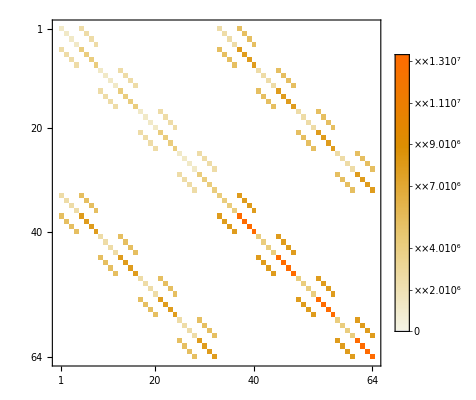

```mathematica
Vdip = (d*e)^2/(4*π*8.85418782×10^-12*11.7*dDip^3*(2π*h));
Hdip = Vdip*TProduct[TProduct[ii, σI, σI], TProduct[ii, σI, σI]];

H2 = TProduct[Hcorrected, IdentityMatrix[8]] + TProduct[IdentityMatrix[8], Hcorrected] + Hdip;

setVariables[]

ΔE = -2000;

MatrixPlot[Hdip, PlotLegends->True]

clearVariables[]
```

### Find evolution operator of two qubits

```mathematica
setVariables[]

Tmax = 1.003*10^-6;

ΔE = -2000;

(* set Eac so it's close to the the |g↓⇓> <-> |e↓⇓> transition *)
Eamp[t_] := 50*tanhWindow[t,Tmax/10,Tmax]^2 ;
ωE = ωE + (Hcorrected[[5, 5]] - Hcorrected[[1, 1]]) - 10^8 /. t->0;

(* turn off oscillatin' magnetic field *)
ωB = (ωB + ωE)/2;
Bamp[t_] := 0

U2 = ConjugateTranspose[TProduct[Urot[[{1, 2}, {1, 2}]], Urot[[{1, 2}, {1, 2}]]]].findEvolutionOperator4D[H2];


clearVariables[]
```

fidelityToCZWithLocalZs[5.75173×10^10,1.003×10^-6]

$Aborted

```mathematica
.
```

### Check the fidelity to a CZ gate

```mathematica
Tmax = 1.003*10^-6;
U2 /. t->Tmax  // MatrixForm

fidelityToCZWithLocalZs[M_] := (
angles = Table[ArcTan[Re[u], Im[u]], {u, Diagonal[M]}];

U2afterGates = U2*E^(-ⅈ*angles[[1]]) /. t->Tmax;

pZ = {{1, 0}, {0, E^(-ⅈ*(angles[[2]] - angles[[1]]))}};
U2afterGates = TProduct[pZ, pZ].U2afterGates;

CZ = DiagonalMatrix[{1, 1, 1, -1}];

fidelity[ConjugateTranspose[CZ].U2afterGates]
)

fidelityToCZWithLocalZs[U2 /. t->Tmax]

U2[[4, 4]]*U2[[1, 1]]/U2[[2, 2]]^2 /. t->Tmax
```

(-0.142279-0.989726 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.954287+0.298738 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.954287+0.298738 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.00207454+0.999996 ⅈ)

0.479914+0. ⅈ

0.733402-0.67978 ⅈ